```mathematica
ϛ[x_,n_]:=If[0==x,0,1/(2n!)Sign[x] x^n]
dβ[x_,n_,d_]:=∑_(k=0)^(n+1) (-1)^k Binomial[n+1,k]ϛ[x+(n+1)/2-k,n-d]
```

```mathematica
w[n_,r_,c_]:=1/(c!)(dβ[(n-1)/2-r,n,c]+1/2 KroneckerDelta[n,c](-1)^(n-r)Binomial[n+1,r+1])
W[n_]:=Table[Table[w[n,r,c],{c,0,n}],{r,0,n}]
```

```mathematica
β[x_,n_]:=Module[{ξ,r,χ},ξ=(n-1)/2-x;r=⌈ξ⌉;χ=r-ξ;w[n,r,0]+∑_(c=1)^n w[n,r,c] χ^c]
```

```mathematica
β[x_,n_]:=Module[{ξ=(n-1)/2-x},If[(n+1)/2<Abs[x],0,W[n]⟦⌈ξ⌉+1,All⟧.Join[{1},Table[(⌈ξ⌉-ξ)^c,{c,1,n}]]]]
```

```mathematica
Sort[Abs[DeleteDuplicates[Chop[Module[{n,x},Table[n=RandomInteger[{1,9}];x=RandomVariate[NormalDistribution[0,√((n+1)/12)]];dβ[x,n,0]-β[x,n],{500}]]]]]]
```

{0}

```mathematica
wint[n_,r_,c_]:=If[0==c,Sum[(1/(q+1))Sum[W[n][[p+(1),q+(1)]],{p,r+1,n}],{q,0,n}],W[n][[r+(1),c-1+(1)]]/c]
Wint[n_]:=Wint[n]=Table[Table[wint[n,r,c],{c,0,n+1}],{r,0,n}]
```

```mathematica
Intβ[x_,n_Integer?NonNegative]:=Which[x<=-(n+1)/2,0,x<(n+1)/2,Block[{ξ=(n-1)/2-x,r},r=⌈ξ⌉;Wint[n][[r+(1)]] . First[VandermondeMatrix[{r-ξ},n+2]]],True,1]
```

```mathematica
Sort[Abs[DeleteDuplicates[Chop[Module[{n,x},Table[n=RandomInteger[{0,9}];x=Clip[RandomVariate[NormalDistribution[0,√((n+1)/12)]],{-(n+1)/2+1.0 10^-5,(n+1)/2-1.0 10^-5}];Quiet[NIntegrate[β[ξ,n],{ξ,-(n+1)/2,x},Method->{Automatic,"SymbolicProcessing"->False},MaxRecursion->3]]-Intβ[x,n],{20}]]]]]]
```

{0,1.11024×10^-10,1.3405×10^-10,3.02191×10^-10,3.24604×10^-10,3.34357×10^-10,1.07657×10^-9,3.17931×10^-7,0.0000518298}

```mathematica
wd[n_,r_,c_]:=(c+1)W[n][[r+(1),c+1+(1)]]
Wd[n_]:=Wd[n]=Table[Table[wd[n,r,c],{c,0,n-1}],{r,0,n}]
```

```mathematica
Dβ[x_,n_Integer?NonNegative]:=Which[(n+1)/2<Abs[x],0,n<=1,∑_(k=0)^(n+1) (-1)^k Binomial[n+1,k]ϛ[x+(n+1)/2-k,n-1],(n+1)/2==Abs[x],0,True,Block[{ξ=(n-1)/2-x,r},r=⌈ξ⌉;Wd[n][[r+(1)]] . First[VandermondeMatrix[{r-ξ},n]]]]
```

```mathematica
Sort[Abs[DeleteDuplicates[Chop[Module[{n,x},Table[n=RandomInteger[{0,9}];x=Clip[RandomVariate[NormalDistribution[0,√((n+1)/12)]],{-(n+1)/2+1.0 10^-5,(n+1)/2-1.0 10^-5}];dβ[x,n,1]-Dβ[x,n],{500}]]]]]]
```

{0}

```mathematica
vβ[n_,m_,p_]:=If[0==p,1,Binomial[m,2p]Sum[((n-1)/2-k)^(2p)dβ[(n-1)/2-k,n,0],{k,0,n-1}]]
Vβ[n_]:=Table[Table[vβ[n,m,p],{p,0,⌊n/2⌋}],{m,1,n}]
```

```mathematica
v[n_,r_,c_]:=If[0==c,1,Binomial[r+1,2c]∑_(k=0)^(n-1) ((n-1)/2-k)^(2c)dβ[(n-1)/2-k,n,0]]
V[n_]:=V[n]=Table[Table[v[n,r,c],{c,0,⌊n/2⌋}],{r,0,n-1}]
```

```mathematica
Table[Vβ[n]-V[n],{n,1,9}]
```

{{{0}},{{0,0},{0,0}},{{0,0},{0,0},{0,0}},{{0,0,0},{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},{{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}},{{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}}}

```mathematica
Sort[Abs[DeleteDuplicates[Chop[Flatten[Table[Table[Table[Module[{x},x=RandomVariate[NormalDistribution[0,√((n+1)/12)]];∑_(k=⌊x⌋-n)^(⌈x⌉+n) k^r dβ[x-k,n,0]-(∑_(c=0)^((r-1)/2) V[n][[r-1+(1),(r-1)/2-c+(1)]] x^(2c+1))],{20}],{r,1,n,2}],{n,1,9}]]]]]]
Sort[Abs[DeleteDuplicates[Chop[Flatten[Table[Table[Table[Module[{x},x=RandomVariate[NormalDistribution[0,√((n+1)/12)]];∑_(k=⌊x⌋-n)^(⌈x⌉+n) k^r dβ[x-k,n,0]-(V[n][[r-1+(1),r/2+(1)]]+∑_(c=1)^(r/2) V[n][[r-1+(1),r/2-c+(1)]] x^(2c))],{20}],{r,2,n,2}],{n,1,9}]]]]]]
```

{0,1.04973×10^-10,1.15844×10^-10,1.33753×10^-10,1.46383×10^-10,1.56842×10^-10,1.58334×10^-10,1.82613×10^-10,1.91423×10^-10,1.94905×10^-10,1.95936×10^-10,1.97973×10^-10,2.15875×10^-10,2.17192×10^-10,2.20497×10^-10,2.37236×10^-10,2.39989×10^-10,2.55564×10^-10,2.58416×10^-10,2.60922×10^-10,2.81136×10^-10,2.86259×10^-10,2.872×10^-10,3.04527×10^-10,3.32869×10^-10,3.60753×10^-10,4.04405×10^-10,4.05571×10^-10,4.14259×10^-10,4.16401×10^-10,4.3629×10^-10,4.96281×10^-10,5.04973×10^-10,5.18598×10^-10,5.23952×10^-10,5.25678×10^-10,5.74783×10^-10,6.5183×10^-10,6.52391×10^-10,6.79917×10^-10,7.33099×10^-10,7.42368×10^-10,7.47919×10^-10,7.49755×10^-10,7.77526×10^-10,7.91247×10^-10,7.95839×10^-10,9.56714×10^-10,9.87995×10^-10,1.00528×10^-9,1.2051×10^-9,1.21772×10^-9,1.25348×10^-9,1.41351×10^-9,1.49754×10^-9,1.54941×10^-9,1.55864×10^-9,1.57356×10^-9,1.61686×10^-9,1.73259×10^-9,1.7356×10^-9,1.74565×10^-9,1.75204×10^-9,1.76788×10^-9,1.8338×10^-9,1.84031×10^-9,1.93288×10^-9,2.00044×10^-9,2.04293×10^-9,2.17107×10^-9,2.17478×10^-9,2.17628×10^-9,2.31213×10^-9,2.31664×10^-9,2.38611×10^-9,2.42719×10^-9,2.52931×10^-9,2.5405×10^-9,2.60248×10^-9,2.63994×10^-9,2.68969×10^-9,2.99216×10^-9,3.02254×10^-9,3.19616×10^-9,3.36803×10^-9,3.41699×10^-9,3.50655×10^-9,3.62617×10^-9,3.86762×10^-9,3.93749×10^-9,3.94006×10^-9,4.08574×10^-9,4.18855×10^-9,4.49795×10^-9,4.54876×10^-9,4.82702×10^-9,5.00051×10^-9,5.05784×10^-9,5.23167×10^-9,5.25025×10^-9,5.48275×10^-9,5.70912×10^-9,7.66489×10^-9,8.56116×10^-9,9.17867×10^-9,9.58597×10^-9,1.01356×10^-8,1.1036×10^-8,1.1398×10^-8,1.18966×10^-8,1.34924×10^-8,1.38101×10^-8,1.49219×10^-8,1.58176×10^-8,1.5948×10^-8,1.62873×10^-8,1.69544×10^-8,1.92879×10^-8,2.04294×10^-8,2.0953×10^-8,2.11732×10^-8,2.25117×10^-8,2.42404×10^-8,3.07348×10^-8,3.07449×10^-8,3.13087×10^-8,3.13454×10^-8,3.6516×10^-8,4.23319×10^-8,4.25881×10^-8,4.36118×10^-8,5.04324×10^-8,5.16886×10^-8,5.41035×10^-8,5.49142×10^-8,5.95663×10^-8,5.99354×10^-8,6.73931×10^-8,7.40328×10^-8,7.66832×10^-8,8.17292×10^-8,8.72835×10^-8,9.66092×10^-8,1.24465×10^-7,1.29274×10^-7,1.32542×10^-7,1.3702×10^-7,1.42561×10^-7,1.43499×10^-7,1.46951×10^-7,1.68238×10^-7,1.77554×10^-7,1.9317×10^-7,1.94641×10^-7,1.98407×10^-7,2.01111×10^-7,2.07494×10^-7,2.0935×10^-7,2.09899×10^-7,2.15907×10^-7,2.18212×10^-7,2.22133×10^-7,2.67602×10^-7,3.09099×10^-7,3.16341×10^-7,3.38384×10^-7,3.54691×10^-7,4.10382×10^-7,4.55017×10^-7,5.00453×10^-7,5.1454×10^-7,6.37203×10^-7,7.2821×10^-7,7.31121×10^-7,7.93181×10^-7,8.0764×10^-7,8.36462×10^-7,8.40307×10^-7,1.14679×10^-6,1.35253×10^-6,1.37851×10^-6,1.40369×10^-6,1.42607×10^-6,1.69225×10^-6,1.88837×10^-6,1.94238×10^-6,1.98751×10^-6,2.26039×10^-6,2.47742×10^-6,2.52796×10^-6,2.56342×10^-6,2.63887×10^-6,2.99498×10^-6,3.02184×10^-6,3.29362×10^-6,3.60824×10^-6,3.6213×10^-6,3.7291×10^-6,3.98278×10^-6,4.3964×10^-6,4.75198×10^-6,4.80357×10^-6,6.00573×10^-6,6.12211×10^-6,6.46776×10^-6,6.55236×10^-6,6.94132×10^-6,7.0209×10^-6,7.8095×10^-6,8.07329×10^-6,8.09837×10^-6,0.0000100394,0.0000108598,0.0000111356,0.0000119628,0.0000127813,0.000012926,0.0000134693,0.0000142567,0.0000162559,0.0000163747,0.0000201334,0.0000212163,0.0000245077,0.0000249963,0.0000255482,0.0000259093,0.0000278733,0.0000283795,0.000032694,0.0000329178,0.0000382961,0.0000395913,0.0000434992,0.0000487404,0.0000524087,0.0000637109,0.000064804,0.0000651524,0.0000807034,0.000106192,0.000109017,0.000122865,0.000139407,0.000159252,0.000160288,0.000163133,0.000191413,0.000206596,0.000224172,0.000246812,0.000369794,0.00075884,0.000895316,0.00093341,0.00099651,0.00106234,0.00115254,0.001174,0.00124018,0.00124276,0.00182641,0.00201849,0.00203094,0.00213005,0.00259297,0.0039487,0.00507468,0.0108562,0.0556219,0.0556689,0.0586682,0.0704229,0.0801255,0.0858188,0.0940909,0.102401,0.11248,0.119995,0.131218,0.171946,0.189304,0.239278,0.344416,0.353412,0.447921,0.45542,0.465988,0.496108}

{0,1.01061×10^-10,1.02078×10^-10,1.05005×10^-10,1.28296×10^-10,1.60645×10^-10,1.70589×10^-10,1.82658×10^-10,1.96497×10^-10,1.96724×10^-10,2.25716×10^-10,2.31859×10^-10,2.32229×10^-10,2.35835×10^-10,2.36052×10^-10,2.4254×10^-10,2.45289×10^-10,2.4533×10^-10,2.58229×10^-10,2.63415×10^-10,2.87379×10^-10,2.87401×10^-10,2.91843×10^-10,2.96208×10^-10,3.0008×10^-10,3.05249×10^-10,3.12502×10^-10,3.44631×10^-10,3.49339×10^-10,3.70038×10^-10,4.16148×10^-10,4.18371×10^-10,5.49952×10^-10,5.54216×10^-10,5.78176×10^-10,8.45794×10^-10,9.04283×10^-10,9.88072×10^-10,1.0467×10^-9,1.23792×10^-9,1.53456×10^-9,1.5936×10^-9,1.5998×10^-9,1.79046×10^-9,1.99301×10^-9,2.03923×10^-9,2.09503×10^-9,2.11955×10^-9,2.19675×10^-9,2.29601×10^-9,2.43321×10^-9,2.65177×10^-9,2.73136×10^-9,2.73186×10^-9,2.79184×10^-9,3.28386×10^-9,3.52821×10^-9,3.6783×10^-9,3.72639×10^-9,3.73529×10^-9,3.94826×10^-9,3.97606×10^-9,4.15531×10^-9,4.20093×10^-9,4.3759×10^-9,4.58924×10^-9,4.64038×10^-9,4.78443×10^-9,4.80208×10^-9,5.31966×10^-9,5.41682×10^-9,5.69793×10^-9,5.72561×10^-9,6.05731×10^-9,6.12786×10^-9,6.20819×10^-9,6.48589×10^-9,6.56962×10^-9,7.31616×10^-9,8.41271×10^-9,8.58204×10^-9,8.58533×10^-9,1.01295×10^-8,1.03184×10^-8,1.085×10^-8,1.122×10^-8,1.15307×10^-8,1.18824×10^-8,1.24383×10^-8,1.257×10^-8,1.29265×10^-8,1.29565×10^-8,1.30234×10^-8,1.46654×10^-8,1.49846×10^-8,1.59797×10^-8,1.61343×10^-8,1.74233×10^-8,1.74436×10^-8,1.79854×10^-8,1.92245×10^-8,1.97712×10^-8,2.01567×10^-8,2.09023×10^-8,2.28666×10^-8,2.37912×10^-8,2.73709×10^-8,2.85365×10^-8,3.1078×10^-8,3.71336×10^-8,4.52624×10^-8,4.55523×10^-8,4.69376×10^-8,4.83411×10^-8,5.05663×10^-8,5.62537×10^-8,5.77198×10^-8,5.78063×10^-8,6.11389×10^-8,6.11774×10^-8,6.11922×10^-8,6.43514×10^-8,6.51934×10^-8,6.6596×10^-8,7.49868×10^-8,8.43795×10^-8,8.58733×10^-8,8.59667×10^-8,9.97241×10^-8,1.00164×10^-7,1.03484×10^-7,1.08263×10^-7,1.10889×10^-7,1.15953×10^-7,1.17525×10^-7,1.36121×10^-7,1.46423×10^-7,1.48384×10^-7,1.67698×10^-7,1.68111×10^-7,1.71837×10^-7,1.81702×10^-7,1.99906×10^-7,2.02097×10^-7,2.09262×10^-7,2.21269×10^-7,2.2655×10^-7,2.60934×10^-7,2.62184×10^-7,2.8612×10^-7,3.21082×10^-7,3.25441×10^-7,3.65263×10^-7,4.22455×10^-7,4.32221×10^-7,4.45789×10^-7,4.55031×10^-7,5.71232×10^-7,6.25981×10^-7,6.28397×10^-7,6.54968×10^-7,6.59793×10^-7,7.41424×10^-7,8.44481×10^-7,8.6546×10^-7,8.86147×10^-7,9.50131×10^-7,9.57977×10^-7,1.05547×10^-6,1.12074×10^-6,1.12627×10^-6,1.17462×10^-6,1.25242×10^-6,1.25463×10^-6,1.36878×10^-6,1.40383×10^-6,1.42087×10^-6,1.42131×10^-6,1.45022×10^-6,1.49626×10^-6,1.8893×10^-6,1.93131×10^-6,2.04876×10^-6,2.1437×10^-6,2.34689×10^-6,2.48664×10^-6,2.48755×10^-6,2.84034×10^-6,2.84863×10^-6,3.30656×10^-6,3.31446×10^-6,3.62479×10^-6,4.29447×10^-6,4.9602×10^-6,9.31617×10^-6,0.000010823,0.0000128818,0.000013645,0.0000137731,0.0000173437,0.0000177001,0.0000178098,0.0000178295,0.0000211188,0.0000219176,0.0000254706,0.0000258149,0.0000372165,0.0000375633,0.0000393505,0.0000448164,0.0000448363,0.0000513361,0.0000521252,0.0000595739,0.0000618141,0.0000804417,0.000101669,0.000109344,0.000115673,0.00011923,0.000124367,0.000162067,0.000175766,0.000178438,0.000209637,0.000211158,0.000272686,0.000274668,0.000330335,0.000402929,0.000433338,0.000452764,0.000502074,0.000680798,0.00100768,0.00109553,0.00113873,0.00122613,0.00122781,0.00138274,0.00153372,0.00164928,0.00169217,0.00174449,0.0017469,0.00184519,0.00196008,0.00254016,0.00267305,0.00324683,0.00349152,0.00351396,0.00360966,0.00370017,0.00375258,0.00459851,0.00756185,0.0114168,0.0134057,0.01428,0.0168459,0.0171449,0.0221697,0.0226743,0.0240058,0.036079,0.0404693,0.056751,0.0570204,0.0857574}

```mathematica
αβ[n_,m_,p_]:=Which[p==m,1,p==m-1,0,True,-Sum[vβ[n,m,q]αβ[n,m-2q,p],{q,1,Floor[(m-p)/2]}]]
αβ[n_,m_]:=Table[αβ[n,m,p],{p,0,m}]
```

```mathematica
a[n_,m_,p_]:=Which[m==p,1,m==p+1,0,True,-∑_(q=1)^⌊(m-p)/2⌋ V[n][[m-1+(1),q+(1)]]a[n,m-2q,p]]
a[n_,m_]:=a[n,m]=Table[a[n,m,p],{p,0,m}]
```

```mathematica
Table[Table[Table[αβ[n,m,p],{p,0,m}],{m,0,n}],{n,0,3}]
Table[Table[Table[a[n,m,p],{p,0,m}],{m,0,n}],{n,0,3}]
```

{{{1}},{{1},{0,1}},{{1},{0,1},{-1/4,0,1}},{{1},{0,1},{-1/3,0,1},{0,-1,0,1}}}

{{{1}},{{1},{0,1}},{{1},{0,1},{-1/4,0,1}},{{1},{0,1},{-1/3,0,1},{0,-1,0,1}}}

```mathematica
Table[Table[αβ[n,m]-a[n,m],{m,0,n}],{n,0,9}]
```

{{{0}},{{0},{0,0}},{{0},{0,0},{0,0,0}},{{0},{0,0},{0,0,0},{0,0,0,0}},{{0},{0,0},{0,0,0},{0,0,0,0},{0,0,0,0,0}},{{0},{0,0},{0,0,0},{0,0,0,0},{0,0,0,0,0},{0,0,0,0,0,0}},{{0},{0,0},{0,0,0},{0,0,0,0},{0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0,0}},{{0},{0,0},{0,0,0},{0,0,0,0},{0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}},{{0},{0,0},{0,0,0},{0,0,0,0},{0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0}},{{0},{0,0},{0,0,0},{0,0,0,0},{0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0}}}

```mathematica
Sort[Abs[DeleteDuplicates[Chop[Flatten[Table[Table[Table[Module[{x},x=RandomVariate[NormalDistribution[0,√((n+1)/12)]];x^m-(∑_(k=-⌊x⌋-n)^(⌈x⌉+n) (a[n,m][[0+(1)]]+∑_(p=1)^(m/2) a[n,m][[2p+(1)]] k^(2p))dβ[x-k,n,0])],{20}],{m,0,n,2}],{n,0,9}]]]]]]
Sort[Abs[DeleteDuplicates[Chop[Flatten[Table[Table[Table[Module[{x},x=RandomVariate[NormalDistribution[0,√((n+1)/12)]];x^m-(∑_(k=-⌊x⌋-n)^(⌈x⌉+n) (∑_(p=0)^((m-1)/2) a[n,m][[2p+1+(1)]] k^(2p+1))dβ[x-k,n,0])],{20}],{m,1,n,2}],{n,0,9}]]]]]]
```

{0,1.0322×10^-10,1.04446×10^-10,1.07957×10^-10,1.09457×10^-10,1.10698×10^-10,1.18628×10^-10,1.26871×10^-10,1.30408×10^-10,1.33528×10^-10,1.35361×10^-10,1.36546×10^-10,1.39383×10^-10,1.43873×10^-10,1.45301×10^-10,1.45401×10^-10,1.47542×10^-10,1.53489×10^-10,1.56953×10^-10,1.57992×10^-10,1.59715×10^-10,1.74655×10^-10,1.77696×10^-10,1.92044×10^-10,1.93017×10^-10,1.95525×10^-10,2.01303×10^-10,2.04009×10^-10,2.14343×10^-10,2.22136×10^-10,2.24837×10^-10,2.32651×10^-10,2.36128×10^-10,2.54412×10^-10,2.67589×10^-10,2.67981×10^-10,3.03709×10^-10,3.04728×10^-10,3.11675×10^-10,3.16616×10^-10,3.25098×10^-10,4.12035×10^-10,4.3849×10^-10,4.66908×10^-10,4.71587×10^-10,5.69743×10^-10,7.21217×10^-10,7.50839×10^-10,8.02012×10^-10,8.14206×10^-10,8.15337×10^-10,1.00682×10^-9,1.0285×10^-9,1.09115×10^-9,1.21836×10^-9,1.33246×10^-9,1.60055×10^-9,1.64463×10^-9,1.69499×10^-9,1.76114×10^-9,1.76624×10^-9,1.83113×10^-9,1.87855×10^-9,1.91577×10^-9,2.01549×10^-9,2.14432×10^-9,2.41742×10^-9,2.65352×10^-9,2.68×10^-9,2.8298×10^-9,2.96885×10^-9,3.10331×10^-9,3.13926×10^-9,3.1888×10^-9,3.28378×10^-9,3.53151×10^-9,3.55084×10^-9,3.5871×10^-9,3.64309×10^-9,3.77875×10^-9,3.80919×10^-9,3.8098×10^-9,4.01155×10^-9,4.09945×10^-9,4.35092×10^-9,4.7805×10^-9,5.0044×10^-9,5.027×10^-9,5.09102×10^-9,5.26807×10^-9,5.82252×10^-9,6.47522×10^-9,7.0604×10^-9,7.07834×10^-9,7.26294×10^-9,7.91354×10^-9,8.13059×10^-9,8.22508×10^-9,8.41827×10^-9,8.81086×10^-9,9.01882×10^-9,9.53076×10^-9,1.00656×10^-8,1.03314×10^-8,1.06709×10^-8,1.10896×10^-8,1.2061×10^-8,1.2225×10^-8,1.25562×10^-8,1.26711×10^-8,1.40111×10^-8,1.45453×10^-8,1.4769×10^-8,1.50826×10^-8,1.54647×10^-8,1.57612×10^-8,1.6292×10^-8,1.71742×10^-8,1.82473×10^-8,1.98232×10^-8,2.18131×10^-8,2.37986×10^-8,2.38586×10^-8,2.53175×10^-8,2.90486×10^-8,3.18167×10^-8,3.25374×10^-8,3.5179×10^-8,3.55278×10^-8,3.60001×10^-8,3.69509×10^-8,3.71778×10^-8,4.13275×10^-8,4.14618×10^-8,4.30901×10^-8,4.64597×10^-8,4.8277×10^-8,5.07222×10^-8,5.38128×10^-8,5.5489×10^-8,6.19155×10^-8,6.26462×10^-8,6.6103×10^-8,6.7554×10^-8,7.14499×10^-8,7.83857×10^-8,7.91797×10^-8,8.53884×10^-8,8.91542×10^-8,8.95749×10^-8,9.49501×10^-8,9.98881×10^-8,1.03165×10^-7,1.08752×10^-7,1.14661×10^-7,1.21135×10^-7,1.29597×10^-7,1.39505×10^-7,1.5112×10^-7,1.64139×10^-7,2.17774×10^-7,2.22877×10^-7,2.30199×10^-7,2.39966×10^-7,2.45288×10^-7,2.51561×10^-7,2.5432×10^-7,2.65446×10^-7,3.28159×10^-7,3.87775×10^-7,3.97262×10^-7,5.64171×10^-7,6.35936×10^-7,6.65292×10^-7,6.95623×10^-7,7.72961×10^-7,8.06921×10^-7,8.99759×10^-7,9.21636×10^-7,9.32233×10^-7,9.89551×10^-7,1.00004×10^-6,1.08385×10^-6,1.18054×10^-6,1.20928×10^-6,1.26805×10^-6,1.28299×10^-6,1.30606×10^-6,1.33088×10^-6,1.3829×10^-6,1.4075×10^-6,1.56438×10^-6,1.60869×10^-6,1.71632×10^-6,1.77499×10^-6,1.86876×10^-6,1.87522×10^-6,2.01023×10^-6,2.27568×10^-6,2.42277×10^-6,2.49404×10^-6,2.592×10^-6,2.77836×10^-6,3.00029×10^-6,3.13722×10^-6,3.67396×10^-6,3.71543×10^-6,4.06013×10^-6,5.28357×10^-6,5.44741×10^-6,6.75543×10^-6,6.84089×10^-6,6.97089×10^-6,6.9735×10^-6,8.40628×10^-6,8.50344×10^-6,8.7941×10^-6,8.95831×10^-6,0.0000109921,0.0000128352,0.0000137354,0.0000161561,0.0000163577,0.000017022,0.0000174284,0.0000226944,0.0000234123,0.0000245818,0.0000253057,0.0000281713,0.0000321343,0.0000408162,0.000045262,0.000065574,0.0000791683,0.0000817273,0.000114461,0.000132839,0.000144949,0.000150064,0.000155636,0.000182081,0.000189951,0.000219921,0.000226627,0.000258025,0.000286168,0.000296642,0.000377748,0.000404792,0.000477171,0.000494374,0.00055202,0.000637671,0.000744721,0.000754256,0.000966507,0.000983723,0.00117026,0.00121301,0.00160171,0.00163937,0.00168461,0.00170126,0.00172604,0.00174155,0.00189874,0.00264131,0.00351708,0.00386094,0.0039135,0.00432841,0.00451251,0.00515288,0.00559613,0.00650273,0.00709312,0.00748011,0.00756434,0.0110353,0.0114794,0.0116998,0.012237,0.0123052,0.0133859,0.0138761,0.0157095,0.0163679,0.0191628,0.021576,0.0267863,0.0305853,0.0335482,0.0391813,0.0444833,0.0824866,0.11498,0.135541,0.157131,0.164928,0.185401,0.19992,0.211433,0.297322,0.301386,0.335663,0.343727,0.373285,0.511711,0.687103,0.995658,1.,1.26541,5.36262}

{0,1.01281×10^-10,1.07406×10^-10,1.09859×10^-10,1.11807×10^-10,1.23899×10^-10,1.25045×10^-10,1.50874×10^-10,1.58642×10^-10,1.63677×10^-10,1.68109×10^-10,1.72543×10^-10,1.94356×10^-10,2.04448×10^-10,2.24458×10^-10,2.35044×10^-10,2.35106×10^-10,2.5044×10^-10,2.5574×10^-10,2.67795×10^-10,2.68915×10^-10,2.872×10^-10,2.89285×10^-10,2.9414×10^-10,3.13637×10^-10,3.33887×10^-10,3.39319×10^-10,3.55916×10^-10,3.62498×10^-10,3.6703×10^-10,3.98119×10^-10,3.98311×10^-10,4.03821×10^-10,4.05764×10^-10,4.18181×10^-10,4.49102×10^-10,4.52955×10^-10,4.589×10^-10,4.77809×10^-10,4.84074×10^-10,4.94934×10^-10,4.95578×10^-10,5.07226×10^-10,5.13407×10^-10,5.85479×10^-10,5.89232×10^-10,5.91885×10^-10,6.17187×10^-10,7.15527×10^-10,7.40481×10^-10,7.51748×10^-10,8.02134×10^-10,8.39684×10^-10,9.66191×10^-10,9.90359×10^-10,1.02217×10^-9,1.05376×10^-9,1.09151×10^-9,1.11781×10^-9,1.17955×10^-9,1.18662×10^-9,1.20251×10^-9,1.32575×10^-9,1.35401×10^-9,1.4257×10^-9,1.48522×10^-9,1.74902×10^-9,1.77494×10^-9,1.78422×10^-9,1.89287×10^-9,1.96378×10^-9,1.99902×10^-9,2.03518×10^-9,2.12032×10^-9,2.19026×10^-9,2.2522×10^-9,2.26779×10^-9,2.29067×10^-9,2.32726×10^-9,2.45312×10^-9,2.84665×10^-9,2.93082×10^-9,3.07584×10^-9,3.09764×10^-9,3.23278×10^-9,3.29992×10^-9,3.82915×10^-9,3.90948×10^-9,3.94676×10^-9,4.0466×10^-9,4.19832×10^-9,4.24667×10^-9,4.29857×10^-9,4.30241×10^-9,4.60883×10^-9,4.92973×10^-9,4.96799×10^-9,5.2174×10^-9,5.69246×10^-9,5.74697×10^-9,5.88319×10^-9,6.0614×10^-9,6.24106×10^-9,7.35647×10^-9,7.5113×10^-9,8.54503×10^-9,9.46617×10^-9,1.01839×10^-8,1.05481×10^-8,1.10217×10^-8,1.12777×10^-8,1.1445×10^-8,1.34321×10^-8,1.59769×10^-8,1.70807×10^-8,1.78404×10^-8,2.02384×10^-8,2.0408×10^-8,2.17875×10^-8,2.41627×10^-8,2.58807×10^-8,2.59309×10^-8,2.63359×10^-8,2.75599×10^-8,2.89159×10^-8,3.21083×10^-8,3.45705×10^-8,3.68028×10^-8,3.68876×10^-8,3.83363×10^-8,3.89567×10^-8,4.04772×10^-8,4.05039×10^-8,4.7201×10^-8,5.07448×10^-8,5.11944×10^-8,5.41335×10^-8,5.71616×10^-8,5.9301×10^-8,6.0648×10^-8,6.28781×10^-8,6.34271×10^-8,6.39994×10^-8,6.40719×10^-8,6.56687×10^-8,7.72669×10^-8,7.85467×10^-8,7.87443×10^-8,1.18033×10^-7,1.21083×10^-7,1.39936×10^-7,1.45184×10^-7,1.5454×10^-7,1.55065×10^-7,1.89603×10^-7,1.95463×10^-7,2.1102×10^-7,2.15314×10^-7,2.31655×10^-7,3.03174×10^-7,3.39297×10^-7,3.53822×10^-7,3.61746×10^-7,3.62061×10^-7,3.84277×10^-7,4.06253×10^-7,4.08211×10^-7,4.12271×10^-7,4.46279×10^-7,4.85081×10^-7,5.21855×10^-7,5.61133×10^-7,7.17252×10^-7,7.31729×10^-7,8.08959×10^-7,9.20389×10^-7,9.87348×10^-7,1.16663×10^-6,1.26794×10^-6,1.2914×10^-6,1.33571×10^-6,1.37166×10^-6,1.37795×10^-6,1.49285×10^-6,1.6785×10^-6,1.79553×10^-6,1.80362×10^-6,1.87853×10^-6,1.93264×10^-6,2.01677×10^-6,2.06045×10^-6,2.30299×10^-6,2.90467×10^-6,2.95139×10^-6,3.05843×10^-6,3.07305×10^-6,3.46138×10^-6,3.69963×10^-6,3.80217×10^-6,4.33917×10^-6,4.36175×10^-6,4.57932×10^-6,4.84666×10^-6,5.92546×10^-6,6.2345×10^-6,6.49014×10^-6,6.97071×10^-6,7.28975×10^-6,7.56095×10^-6,7.70551×10^-6,7.72193×10^-6,8.08697×10^-6,8.28145×10^-6,8.70855×10^-6,8.86042×10^-6,9.51963×10^-6,0.000010978,0.0000112983,0.0000146531,0.0000148087,0.0000156203,0.0000169282,0.0000208958,0.0000229378,0.0000231186,0.0000269689,0.0000365138,0.0000529677,0.0000535489,0.0000544998,0.0000578396,0.0000594124,0.0000687202,0.0000707044,0.0000782979,0.0000931871,0.000104847,0.000111642,0.000112861,0.000123159,0.000133455,0.000158914,0.000206379,0.000254578,0.000282234,0.000283403,0.000287405,0.000291257,0.000334719,0.000359529,0.000596606,0.000698036,0.000882039,0.000915182,0.000935369,0.00104618,0.00104961,0.00140337,0.00156218,0.00163526,0.00178541,0.00197798,0.00246473,0.00249521,0.00346726,0.0036625,0.003721,0.00377346,0.00409962,0.00625016,0.0083878,0.0099742,0.0130264,0.0133627,0.016227,0.0174183,0.0198756,0.0209377,0.0221014,0.0308876,0.0764474,0.0814962,0.0918235,0.0972793,0.114143,0.142333,0.181019,0.24095,0.257506,0.26695,0.291411,0.300971,0.340026,0.34751,0.467366,0.485526,0.515558,0.547212,0.676289,0.69627,1.20092,1.38281,32.5596,37.9823}

```mathematica
Zβ[n_Integer?NonNegative]:=Zβ[n]=N[Which[0==n,{},1==n,{},2==n,{-3+2Sqrt[2]},3==n,{-2+Sqrt[3]},4==n,{-19+Sqrt[304]+Sqrt[664-Sqrt[438976]],-19-Sqrt[304]+Sqrt[664+Sqrt[438976]]},5==n,{-13/2+Sqrt[105/4]+Sqrt[135/2-Sqrt[17745/4]],-13/2-Sqrt[105/4]+Sqrt[135/2+Sqrt[17745/4]]},6==n,Block[{θ=ArcCos[-668791/Sqrt[447872715451]]/3,c,s,λ1,λ2,λ3},c=Sqrt[122416/9]Cos[θ];s=Sqrt[122416/3]Sin[θ];λ1=361/3-2c;λ2=361/3+c-s;λ3=361/3+c+s;{Sqrt[λ1^2-1]-λ1,Sqrt[λ2^2-1]-λ2,Sqrt[λ3^2-1]-λ3}],7==n,Block[{θ=ArcCos[-738/Sqrt[556549]]/3,c,s,λ1,λ2,λ3},c=Sqrt[301]Cos[θ];s=Sqrt[903]Sin[θ];λ1=20-2c;λ2=20+c-s;λ3=20+c+s;{Sqrt[λ1^2-1]-λ1,Sqrt[λ2^2-1]-λ2,Sqrt[λ3^2-1]-λ3}],8==n,Block[{θ=ArcCos[Sqrt[3191438329707/3435302785852]]/3,λ0,λ,ρ,ν1,ν2,μ1,μ2,μ3,μ4},λ0=Sqrt[656944+Sqrt[106853376]Cos[θ]];λ=1300071/2-λ0^2;ρ=1638λ0-Sqrt[4λ^2-250737];ν1=Sqrt[2641593/2+λ-ρ];ν2=Sqrt[2641593/2+λ+ρ];μ1=-819+λ0+ν1;μ2=-819+λ0-ν1;μ3=-819-λ0+ν2;μ4=-819-λ0-ν2;{μ1+Sqrt[μ1^2-1],μ2+Sqrt[μ2^2-1],μ3+Sqrt[μ3^2-1],μ4+Sqrt[μ4^2-1]}],9==n,Block[{θ=ArcCos[Sqrt[607973645/699281408]]/3,λ0,λ,ρ,ν1,ν2,μ1,μ2,μ3,μ4},λ0=Sqrt[53265/16+Sqrt[146160]Cos[θ]];λ=48397/16-λ0^2;ρ=(251/2)λ0-Sqrt[4λ^2-7936];ν1=Sqrt[55699/8+λ-ρ];ν2=Sqrt[55699/8+λ+ρ];μ1=-251/4+λ0+ν1;μ2=-251/4+λ0-ν1;μ3=-251/4-λ0+ν2;μ4=-251/4-λ0-ν2;{μ1+Sqrt[μ1^2-1],μ2+Sqrt[μ2^2-1],μ3+Sqrt[μ3^2-1],μ4+Sqrt[μ4^2-1]}],True,Block[{z},Sort[Map[2/(#-Sqrt[#^2-4])&,SolveValues[0==(dβ[0,n,0]+2Sum[dβ[2q,n,0](-1)^q,{q,1,Floor[Floor[n/2]/2]}])+Sum[(-1)^p z^(2p+1)Sum[(-1)^q dβ[2q+1,n,0](2q+1)(q+p)!/(q-p)!,{q,p,Floor[(Floor[n/2]-1)/2]}]/(2p+1)!,{p,0,Floor[Floor[n/2]/2]}]+Sum[(-1)^p z^(2p)Sum[(-1)^q dβ[2q,n,0]2q (q+p)!/((q+p)(q-p)!),{q,p,Floor[Floor[n/2]/2]}]/(2p)!,{p,1,Floor[Floor[n/2]/2]}],z]],Less]]]]
ιβ[n_]:=With[{v=W[n].First[VandermondeMatrix[{Mod[n+1,2]/2},n+1]]},LeastSquares[Table[v.Table[Map[#^Abs[k+Floor[Ξ-(n-1)/2]]&,Zβ[n]],{k,0,n}],{Ξ,0,Floor[n/2]-1}],Join[{1},Table[0,Floor[n/2]-1]]]]
```

```mathematica
Table[ιβ[n],{n,0,9}]//MatrixForm
```

LeastSquares::matrix: Argument {} at position 1 is not a non-empty rectangular matrix.

(LeastSquares[{},{1}]
LeastSquares[{},{1}]
{1.41421}
{1.73205}
{2.28832,-0.0755861}
{3.09499,-0.252816}
{4.28378,-0.55712,0.000133106}
{6.01628,-1.05582,0.00426918}
{8.55164,-1.85473,0.0261961,-5.91406×10^-9}
{12.2697,-3.126,0.0929633,-7.85095×10^-6})

```mathematica
Chop[Table[Table[∑_(q=k-⌊n/2⌋)^(k+⌊n/2⌋) (∑_(p=0)^(Length[ιβ[n]]-1) ιβ[n][[p+(1)]](Zβ[n][[p+(1)]])^Abs[q])β[k-q,n],{k,-5,5}],{n,2,9}]]
```

{{0,0,0,0,0,1.,0,0,0,0,0},{0,0,0,0,0,1.,0,0,0,0,0},{0,0,0,0,0,1.,0,0,0,0,0},{0,0,0,0,0,1.,0,0,0,0,0},{0,0,0,0,0,1.,0,0,0,0,0},{0,0,0,0,0,1.,0,0,0,0,0},{0,0,0,0,0,1.,0,0,0,0,0},{0,0,0,0,0,1.,0,0,0,0,0}}

```mathematica
Chop[Table[ιβ[n]-Inverse[Table[Table[∑_(q=-⌊n/2⌋)^⌊n/2⌋ (Zβ[n][[c+(1)]])^Abs[r-q] β[q,n],{c,0,⌊n/2⌋-1}],{r,0,⌊n/2⌋-1}]][[All,1]],{n,2,9}]]
```

{{0},{0},{0,0},{0,0},{0,0,0},{0,0,0},{0,0,0,0},{0,0,0,0}}

```mathematica
Ibβ[k_Integer,n_Integer?NonNegative]:=If[n<=1,DiscreteDelta[k],ιβ[n].Map[#^Abs[k]&,Zβ[n]]]
```

```mathematica
db0[x_,n_,d_]:=Module[{ξ,r,χ},ξ=(n-1)/2-x;r=⌈ξ⌉;χ=r-ξ;d!SplineKit`SplineUtilities`Private`Wβ[n][[r+(1),d+(1)]]+∑_(c=d+1)^n (c!)/((c-d)!)SplineKit`SplineUtilities`Private`Wβ[n][[r+(1),c+(1)]] χ^(c-d)]
```

```mathematica
Chop[Module[{x,n,d},Table[n=RandomInteger[{2,9}];d=RandomInteger[{0,n-1}];x=RandomReal[{-(n+1)/2,(n+1)/2}];Diffβ[x,n,d]-db0[x,n,d],{300}]]]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

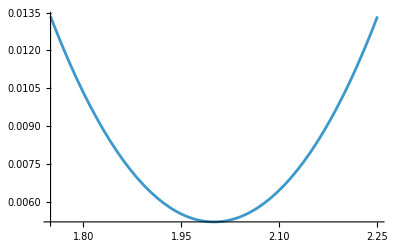

```mathematica
Plot[∑_(p=-20)^20 dβ[p #+x,4,0],{x,1.75,2.25}]&[4]
```